```mathematica
encodeID[expr_]:=StringReplace[Developer`EncodeBase64@BinarySerialize@expr,"/"->"~"]
decodeID[expr_]:=BinaryDeserialize@Developer`DecodeBase64ToByteArray@StringReplace[expr,"~"->"/"]
```

```mathematica
ClearAll[getFileNames,fromFileNameGetGeoRange]

getFileNames[folderName_] := 
	FileNames["*.png",FileNameJoin[{NotebookDirectory[],folderName}],Infinity];

fromFileNameGetGeoRange[fileName_] := 
	decodeID[FileBaseName@fileName]["GeoRange"];
```

```mathematica
ClearAll[associateFilesToGeoRange]
associateFilesToGeoRange[fileNames_] := 
	Map[
		File[#] -> fromFileNameGetGeoRange[#] &,
		getFileNames[fileNames]
	]
```

```mathematica
calculateError[net_,data_] :=(Abs[net[data[[All,1]]]-data[[All,2]]])/data[[All,2]]//Mean
calculateMeanSq[net_,data_] :=(Abs[net[data[[All,1]]]-data[[All,2]]])^2//Mean
```

```mathematica
ClearAll[sortPerformance]
sortPerformance[net_,data_] := 
	With[
		{img = Map[Import,data[[All,1]]], correspondingScale = data[[All,2]]},
		SortBy[
			AssociationThread[img,Transpose[{net[img],correspondingScale}]],
			Abs[First[#] - Last[#]]&
		]
	]
```

Training | Validation | Testing
9814 | 1050 | 420

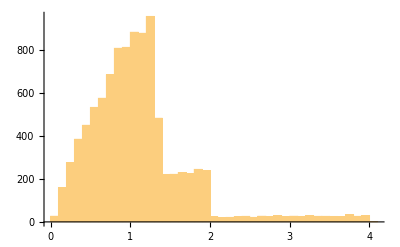
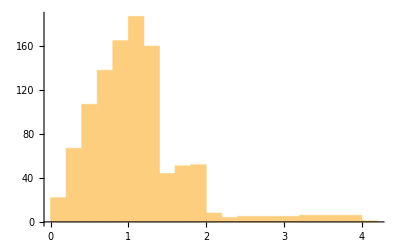
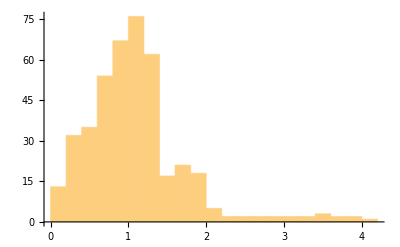
Training Data distribution | Validation Data distribution | Testing Data distribution
-Graphics- | -Graphics- | -Graphics-

```mathematica
ClearAll[training2,validation2,testing2]

training2 = RandomSample@associateFilesToGeoRange["training"];
validation2 = RandomSample@associateFilesToGeoRange["validation"];
testing2 = RandomSample@associateFilesToGeoRange["testing"];

TableForm[
	{{"Training","Validation","Testing"},
	{Length@training2,Length@validation2,Length@testing2}}
]

TableForm[
	{{"Training Data distribution","Validation Data distribution","Testing Data distribution"},
	{Histogram[Sort@training2[[All,2]],PlotRange->All],Histogram[Sort@validation2[[All,2]],PlotRange->All],Histogram[Sort@testing2[[All,2]],PlotRange->All]}}
]
```

```mathematica
ClearAll[tnet2]
tnet2 = Import["/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/wolframScriptCodes/moreImagesToTrain/amazonTrainedNet.wlnet"]
(*tnet = Import["/Users/mehmetsahin/Desktop/wolframscpt/more/moreImagesToTrain/progress/2018-07-09T20:54:19_0_30_12270_1.04e-2_4.34e-2.wlnet"]*)
```

NetChain[<>]

```mathematica
ClearAll[dataset2]
dataset2 = sortPerformance[tnet2,testing2];
Normal@dataset2[[1;;4]]  (*Best 3*)
Normal@dataset2[[-4;;]] (*Worst 3*)
```

{-Graphics-→{1.14055,1.13986},-Graphics-→{1.28119,1.28017},-Graphics-→{1.04051,1.04159},-Graphics-→{0.6932,0.694391}}

{-Graphics-→{0.468719,1.30694},-Graphics-→{2.20637,3.05436},-Graphics-→{2.80508,3.84052},-Graphics-→{3.13268,1.83812}}

```mathematica
Column[{Row[
	{Style["Best->   ",14,Bold],First@dataset2[[1]],
	Column[{Style[Row[
	{"Real Scale:   ",ToString@First@Last@dataset2[[1]]}],13],
	Style[Row[
	{"Predicted :   ",ToString@Last@Last@dataset2[[1]]}],13],Style[Row[
	{"Error     :   ","0.04%"}],13]}],"    ",Column[{First@dataset2[[2]],
	Style[Row[
	{"Real Scale:   ",ToString@First@Last@dataset2[[2]]}],13],
	Style[Row[
	{"Predicted :   ",ToString@Last@Last@dataset2[[2]]}],13],Style[Row[
	{"Error     :   ","0.15%"}],13]}]}
],"   ",Row[
	{Style["Worst->  ",14,Bold],Column[{First@dataset2[[-1]],
	Style[Row[
	{"Real Scale:   ",ToString@First@Last@dataset2[[-1]]}],13],
	Style[Row[
	{"Predicted :   ",ToString@Last@Last@dataset2[[-1]]}],13],Style[Row[
	{"Error     :   ","41.37%"}],13]}],"    ",Column[{First@dataset2[[-2]],
	Style[Row[
	{"Real Scale:   ",ToString@First@Last@dataset2[[-2]]}],13],
	Style[Row[
	{"Predicted :   ",ToString@Last@Last@dataset2[[-2]]}],13],Style[Row[
	{"Error     :   ","42.74%"}],13]}]}
]}]
```

First::normal: Nonatomic expression expected at position 1 in First[1.13986].

Last::normal: Nonatomic expression expected at position 1 in Last[1.13986].

First::normal: Nonatomic expression expected at position 1 in First[1.28017].

Last::normal: Nonatomic expression expected at position 1 in Last[1.28017].

First::normal: Nonatomic expression expected at position 1 in First[1.83812].

General::stop: Further output of First::normal will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[1.83812].

General::stop: Further output of Last::normal will be suppressed during this calculation.

Best->   1.14055Real Scale:   First[1.13986]
Predicted :   Last[1.13986]
Error     :   0.04%    1.28119
Real Scale:   First[1.28017]
Predicted :   Last[1.28017]
Error     :   0.15%
   
Worst->  3.13268
Real Scale:   First[1.83812]
Predicted :   Last[1.83812]
Error     :   41.37%    2.80508
Real Scale:   First[3.84052]
Predicted :   Last[3.84052]
Error     :   42.74%

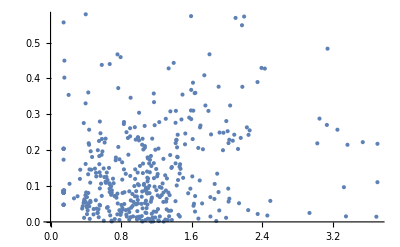

```mathematica
ListPlot[Transpose[{Map[First[#]&,Values[dataset2]],Map[Abs[First[#]-Last[#]]&,Values[dataset2]]}]]
```

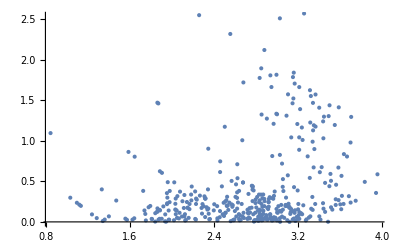

```mathematica
ListPlot[Transpose[{Map[First[#]&,Values[dataset2]],Map[Abs[First[#]-Last[#]]&,Values[dataset2]]}]]
```

```mathematica
calculateError[tnet,testing]
```

0.205119